```mathematica
results=Table[
population = RandomVariate[NormalDistribution[0,1],1000];
{
Mean[population],
Median[population]
},
100000
];
```

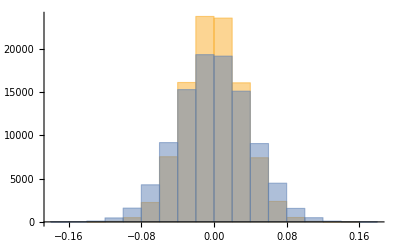

```mathematica
Histogram[
Transpose[results]
]
```

https://en.wikipedia.org/wiki/Fat-tailed_distribution

```mathematica
results=Table[
population = RandomVariate[CauchyDistribution[0,1],1000];
{
Mean[population],
Median[population]
},
100000
];
```

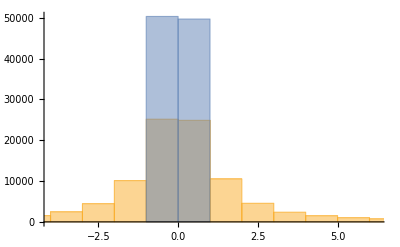

```mathematica
Histogram[
Transpose[results],
{1}
]
```